## Magnetic Feshbach resonance with square well model

We now have an N-channel square well model coded up in “MyNchannelSqrWell?.nb”  Let’s start with a 2-channel model and rig-up a magnetic Feshbach resonance by mapping the channel separation (Zeeman splitting) to the magnetic field.

### Find an approximate function for the energy.

Let’s start with the single-channel s-wave transcendental equation for the bound-state energy.

```mathematica
TEQ0[r0_,v0_,ϵ_]:=√(v0+ϵ) Cos[r0 √(v0+ϵ)]+√-ϵ Sin[r0 √(v0+ϵ)]
```

When the energy is zero,

```mathematica
TEQ0[1,v0,0]
```

√v0 Cos[√v0]

suggests √v_0=1/2 π, 3/2 π,...

so v_0=(n+1/2)^2 π^2 with n=0,1,2,...

Solving this for n gives the approximate number of bound states as a function of the depth v_0:

n=(√v_0)/π-1/2

The number of bound states is n+1:

```mathematica
Plot[Floor[(√v0)/π+1/2],{v0,0,500},Frame->True,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","# of bound states"},LabelStyle->Large];
```

This is quite useful because we can immediately estimate the total density of states for an N-channel problem by noting that the total number of bound states in the uncoupled limit is:

n_tot=∑_i ((V_(i i)+ϵ_i^th)/π+1/2)

ρ=1/(∑_i ((V_(i i)+ϵ_i^th)/π+1/2))

where V_(i i)+ϵ_i^th=D_i is the total depth of the ith channel.

The energies may be easily plotted as a contour plot.  And compared to the approximate energies from the infinite square well:

√((2μ)/ℏ^2(E+V_0)) r_0=n π

ϵ =n^2 π^2-v_0

```mathematica
Table[√(ϵ+v0)==n π,{n,1,4}]
```

{√(v0+ϵ)==π,√(v0+ϵ)==2 π,√(v0+ϵ)==3 π,√(v0+ϵ)==4 π}

A lower bound is found by setting the phase accumulated inside the well to be ϕ=n π-π/2 with n=1,2,3.... This estimate gives the exact energy only for those states with eigen-energy equal to zero, so that an odd multiple of π/2 phase is accumulated inside the well, and there is an infinitely long exponential tail outside the well (since a→∞).  As the state becomes more deeply bound, more an more of the wavefunction is drawn into the well and the exponential tail shrinks.  The additional confinement can only raise the energy.

An upper bound is provided by the condition that the exponential tail has shrunk to zero so that we have an approximation to the infinite square well: ϕ=n π.

At threshold, the v_0 values corresponding to a zero-energy state are:

v_0=(n+1/2)^2 π^2

with n=0,1,2,...

The slope of the ϵ vs. v_0 asymptotically must approach ⅆϵ/(ⅆ v_0)=-1.  Let’s use instead the binding energy B=|ϵ|.

We deduce that the exact energy for the mth state (m=1,2,3...) must be bounded by the lines:

ϵ_lower=(m-1/2)^2 π^2-v_0

```mathematica
ϵlower[m_,v0_]:=(m-1/2)^2 π^2-v0
```

ϵ_upper=m^2 π^2-v_0

```mathematica
ϵupper[m_,v0_]:=m^2 π^2-v0
```

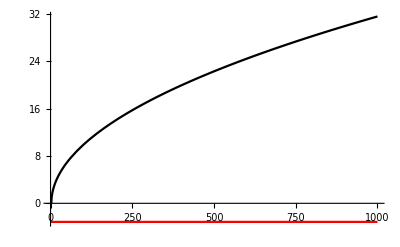

```mathematica
m=1;Plot[{TEQ0[1,vtest,ϵlower[m,vtest]],TEQ0[1,vtest,ϵupper[m,vtest]]},{vtest,0,1000},PlotStyle->{Black,Red}]
```

```mathematica
vmax=100;
```

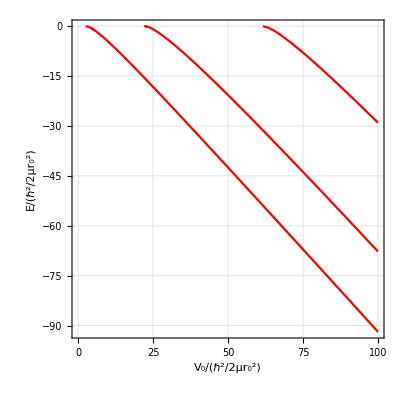

```mathematica
pexact=ContourPlot[{TEQ0[1,v0,ϵ]==0},{v0,0,vmax},{ϵ,-v0+2,0},LabelStyle->Large,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","E/(ℏ^2/2μr_0^2)"},GridLines->Automatic,ContourStyle->{Red}]
```

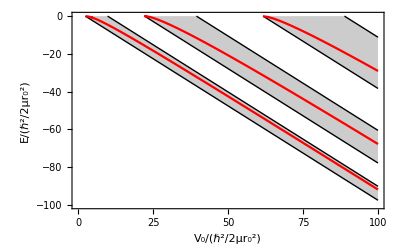

```mathematica
plim=Show[{Table[Plot[{ϵlower[m,v0],ϵupper[m,v0]},{v0,0,vmax},Filling->{1->{2}},PlotStyle->{{Black,Thin},{Black,Thin}},PlotRange->{{0,vmax},{-vmax,0}},Frame->True,LabelStyle->Large,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","E/(ℏ^2/2μr_0^2)"}],{m,1,10}],pexact}]
```

### How to set up the potential...

In order to construct a model more easily, I’d like to create a function that simply returns the value of the potential depth needed to place an energy at a particular place.

Let’s assume we’re talking about the ground state.  Then using the average of the lower and upper bound as a starting point for the root-finder, we have:

```mathematica
TEQ0[1,v0,ϵ]
```

√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)]

```mathematica
FortranForm[Simplify[D[TEQ0[1,v0,energy],energy]]]
```

((Sqrt(-energy) - energy)*Cos(Sqrt(energy + v0)) - (1 + Sqrt(-energy))*Sqrt(energy + v0)*Sin(Sqrt(energy + v0)))/(2.*Sqrt(-energy)*Sqrt(energy + v0))

Determine the potential depth that yields the nth state with binding energy B

```mathematica
v0Depth[B_,n_]:=v0/.FindRoot[√(v0-B) Cos[√(v0-B)]+√B Sin[√(v0-B)]==0,{v0,((n-1/2)^2+n^2)/2 π^2+B}]
```

```mathematica
Energy[v0_,n_,ϵth_]:=ϵ+ϵth/.FindRoot[√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)]==0,{ϵ,((n-1/2)^2+n^2)/2 π^2-v0}]
```

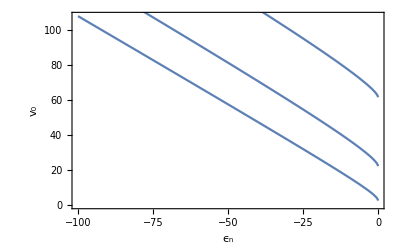

```mathematica
Show[Table[Plot[v0Depth[-ϵ,n],{ϵ,-vmax,0},Frame->True,FrameLabel->{"ϵ_n","v_0"},LabelStyle->Large],{n,1,10}]]
```

This seems to work very well.

Let’s plot some potentials and energies with threshold offsets.  Let’s first just plot the square-well potential

I’ll set the closed channel depth equal to something that gives a binding at around B=100 ℏ^2/(2μ r_0^2), then just shift the entire closed channel up and down to move the resonance position.

```mathematica
B0=100;vClosed=v0Depth[B0,1];
```

```mathematica
Vfun[r_,V0_,eth_]:=Piecewise[{{-V0+eth,r<1},{eth,r≥1}}]
```

```mathematica
Manipulate[Plot[{ϵopen,
Energy[v0Depth[-ϵopen,1],2,0],
Energy[v0Depth[-ϵopen,1],3,0],
Vfun[r,v0Depth[-ϵopen,1],0],
ϵshift,
Vfun[r,vClosed,B0+ϵshift]
},
{r,0,1.2},PlotRange->{-100,B0+20},PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black},{Red,Dashed},{Red}},Frame->True,LabelStyle->Large,Exclusions->None,FrameLabel->{"r/r_0","V(r)/(ℏ^2/2μr_0^2)"}],{ϵopen,-90,0},{ϵshift,-10,10}];
```

General::prng: Value of option PlotRange -> {-100,20+B0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Cool.  Now I want to add a third channel that places the an excited state resonance near threshold.  To do this, I determine the depth necessary:

```mathematica
vClosed1=v0Depth[B0,2]
```

133.184

Space the resonances by a typical spacing D_0

```mathematica
D0=1;
```

Let’s define a function that will construct the diagonal part of the potential matrix and the thresholds.

```mathematica
MakeVDiag[NumChan_,NumOpen_,NumEven_,
BClosedEven_,nClosedEven_,BClosedOdd_,nClosedOdd_,
ϵOpen_,nOpen_]:=
Module[{i,vClosedE,vClosedO,vOpen,vDiag,ϵth},
vClosedE=v0Depth[BClosedEven,nClosedEven];
vClosedO=v0Depth[BClosedOdd,nClosedOdd];
vOpen=v0Depth[-ϵOpen,nOpen];
vDiag=Table[Which[i<=NumEven,-vClosedE+BClosedEven,NumEven<i≤NumChan-1,-vClosedO+BClosedOdd,i==NumChan,-vOpen],{i,1,NumChan}];
ϵth=Table[Which[i≤NumEven,BClosedEven,NumEven<i≤NumChan-1,BClosedOdd,i==NumChan,0],{i,1,NumChan}];
{vDiag,ϵth}
]
```

```mathematica
MatrixForm[MakeVDiag[3,2,1,100,1,100,2,-10,1]]
```

(-8.19547 | -33.184 | -16.136
100 | 100 | 0)

```mathematica
D0=2;
Manipulate[Plot[{ϵopen,
Vfun[r,v0Depth[-ϵopen,1],0],
Energy[v0Depth[-ϵopen,1],2,0],
ϵshift,
Vfun[r,vClosed,B0+ϵshift],
ϵshift+D0,
Vfun[r,vClosed1,B0+ϵshift+D0]},{r,0,1.2},PlotRange->{-90,B0+20},PlotStyle->{{Black,Dashed},{Black},{Black,Dashed},{Red,Dashed},{Red},{Blue,Dashed},{Blue}},Frame->True,LabelStyle->Large,Exclusions->None,FrameLabel->{"r/r_0","V(r)/(ℏ^2/2μr_0^2)"}],{ϵopen,-60,0},{ϵshift,-10,10}];
```

General::prng: Value of option PlotRange -> {-90,20+B0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

A magnetic Feshbach resonance is modeled by letting the position of the uncoupled bound states be:

ϵ_i(B)=ϵ_i(0)+α_i B

with α_i=(∂ϵ_i)/(∂B) tuned to give the correct density of magnetic Feshbach resonances.  For simplicity let’s assume that α is independent of i, α_i=α.  It should correspond to the slope of the Zeeman shift for these levels, since the density of states in each channel potential is only 1/V_0 in our model, we must include many many more channels to reproduce the .

One immediate question is: are the resonance line-shapes different for the two resonances?  We are also interested in the effect of the open channel resonance. And what happens as the number of bound states increases?  Do the resonances become narrower or broader?

Perhaps we should try a 3-channel model with

V=(-V_C1+ϵ_1(B) | 0 | γ
0 | -V_C2+ϵ_2(B) | γ
γ | γ | -V_open(B))

ϵ_th=(ϵ_1(B) | ϵ_2(B) | 0)

### Now on to the magnetic Feshbach resonance...

#### Setup

Solutions of just the diagonal operator are:

```mathematica
f[L_,k_,r_]=√(π/2 k r)BesselJ[L+1/2,k r];
```

```mathematica
df[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselJ[L+1/2,k r],r]];
```

```mathematica
g[L_,k_,r_]=√(π/2 k r)BesselY[L+1/2,k r];
```

```mathematica
dg[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselY[L+1/2,k r],r]];
```

I’ll multiply the decaying function by a constant to rescale it for the strongly closed channels.

```mathematica
gb[L_,κ_,r_]=√(2/π κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0;
```

```mathematica
dgb[L_,κ_,r_]=Simplify[D[gb[L,κ,r],r]];
```

```mathematica
fb[L_,κ_,r_]=√(2/π κ r)BesselI[L+1/2,κ r];
```

```mathematica
dfb[L_,κ_,r_]=Simplify[D[√(2/π κ r)BesselI[L+1/2,κ r],r]];
```

```mathematica
vO1=v0Depth[0,1];vO2=v0Depth[0,2];
SetupPotentialOpenClosed[NumChan_,NumEven_,B02_,Bfield_,γ_,ϵi0_]:=
Module[{i,j,α,BE,ϵthresh,Λvals,U,V,B01,ΔVres},
BE=100;
ΔVres=5;
α=ΔVres/B02;
B01=0;
vClosed=v0Depth[BE,1];
vClosed1=v0Depth[BE,2];
ϵthresh=Table[If[i==NumChan,0,BE+ϵi0[[i]]+α Bfield],{i,1,NumChan}];
V=Table[0,{i,1,NumChan},{j,1,NumChan}];
Do[V[[i,i]]=-vClosed+BE+ϵi0[[i]]+α (Bfield),{i,1,NumEven}];
Do[V[[i,i]]=-vClosed1+BE+ϵi0[[i]]+α (Bfield),{i,NumEven+1,NumChan-1}];
V[[NumChan,NumChan]]=-vO1-((vO2-vO1)/B02)Bfield;
(*V[[NumChan,NumChan]]=-v0Depth[-ϵopen,1]+α Bfield;*)
Do[V[[i,NumChan]]=γ;V[[NumChan,i]]=γ,{i,1,NumChan-1}];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
{Λvals,U,ϵthresh,V}
]
```

```mathematica
pot1=SetupPotentialOpenClosed[3,1,-10,0,0.5,{1,2}];
```

Let’s check if this makes sense:

```mathematica
MatrixForm[pot1[[4]]]
pot1[[3]]
```

(-7.19547 | 0 | 0.5
0 | -31.184 | 0.5
0.5 | 0.5 | -2.4674)

{101,102,0}

looks sensible.

```mathematica
ϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,f[L,√(Energy-λsqr),r],fb[L,√(λsqr-Energy),r]];
dϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,df[L,√(Energy-λsqr),r],dfb[L,√(λsqr-Energy),r]];
```

```mathematica
MakeΦMat[NumChan_,L_,Λ_,U_,Energy_,r_]:=Module[
{Φ,dΦ,i,j},
Φ=Table[U[[i,j]]ϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
dΦ=Table[U[[i,j]]dϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
{Φ,dΦ}
]
```

```mathematica
SetupABMatNew[NumChan_,NumOpen_,ϵthresh_,Φ_,dΦ_,L_,r_,Energy_]:=
Module[{i,j,SizeAB,κc,ko,NumClosed,ABmat,bvec},
SizeAB=2 NumChan+1;
NumClosed=NumChan-NumOpen;
ABmat=Table[0,{i,1,SizeAB},{j,1,SizeAB}];
(*Closed Channels Interior*)

Do[
ABmat[[2 i-1,1;;NumChan]]=Φ[[i]];
ABmat[[2 i,1;;NumChan]]=dΦ[[i]];,
{i,1,NumClosed}
];
(*Open Channel Interior*)
ABmat[[2 NumChan-1,1;;NumChan]]=Φ[[NumChan]];ABmat[[2 NumChan,1;;NumChan]]=dΦ[[NumChan]];

(*Closed Channels Exterior*)
Do[
κc=√(ϵthresh[[i]]-Energy);ABmat[[2i-1,NumChan+i]]=-gb[L,√(ϵthresh[[i]]-Energy),r];
ABmat[[2 i,NumChan+i]]=-dgb[L,√(ϵthresh[[i]]-Energy),r];,
{i,1,NumClosed}];

(*Open Channel Exterior*)
ko=√(Energy-ϵthresh[[NumChan]]);
ABmat[[2 NumChan-1,NumChan+NumClosed+1]]=f[L,ko,r];
ABmat[[2 NumChan-1,NumChan+NumClosed+2]]=-g[L,ko,r];
ABmat[[2 NumChan,NumChan+NumClosed+1]]=df[L,ko,r];
ABmat[[2 NumChan,NumChan+NumClosed+2]]=-dg[L,ko,r];

(* Pick the open channel amplitude to be 1 *)
ABmat[[SizeAB,NumChan+NumClosed+1]]=1; 
bvec=Table[0,{i,SizeAB}];
bvec[[SizeAB]]=1;

{ABmat,bvec}
]
```

```mathematica
SolutionData[NumChan_,NumOpen_,ϵthresh_,sols_,L_,r_,Energy_]:=Module[
{ascat,sigma,aclose,aLsqr,norm,δOverπ,coef,σ,i,j,δ,SizeAB,tandel},

SizeAB=2NumChan+1;
tandel=sols[[SizeAB]]/sols[[SizeAB-1]];
ascat=-tandel/√Energy;
norm=1/(√(sols[[SizeAB-1]]^2+sols[[SizeAB]]^2));
δ=ArcTan[tandel];
δOverπ=δ/π;
aclose=sols[[NumChan+1;;2NumChan-1]];
coef=sols[[1;;NumChan]];
σ=(4π Sin[δ]^2)/Energy;
aLsqr=Sin[δ]^2;
{ascat,δOverπ,aLsqr,norm,aclose,coef}]
```

```mathematica
RunEnergyLoop[NumChan_,NumOpen_,L_,rmatch_,Λ_,U_,ϵth_,Energy_]:=Module[
{Φ,dΦ,AB,b,sols,data},
{Φ,dΦ}=MakeΦMat[NumChan,L,Λ,U,Energy,rmatch];
{AB,b}=SetupABMatNew[NumChan,NumOpen,ϵth,Φ,dΦ,L,rmatch,Energy];
sols=LinearSolve[AB,b];
data=SolutionData[NumChan,NumOpen,ϵth,sols,L,rmatch,Energy];
data
]
```

```mathematica
BSTEQ[Energy_,Λ_,U_,L_,ϵth_,rmatch_,NumClosed_]:=Module[{i,j,Gmat,Φ,dΦ},
Gmat=Table[0,{i,1,NumClosed},{j,1,NumClosed}];
Do[Gmat[[i,i]]=dgb[L,√(ϵth[[i]]-Energy),rmatch]/gb[L,√(ϵth[[i]]-Energy),rmatch],{i,1,NumClosed}];
{Φ,dΦ}=MakeΦMat[NumClosed,L,Λ,U,Energy,rmatch];
Φ=Φ[[1;;NumClosed,1;;NumClosed]];
dΦ=dΦ[[1;;NumClosed,1;;NumClosed]];
Det[dΦ-Gmat.Φ]
]
```

```mathematica
RunMagneticLoop[NumChan_,NumOpen_,NumEven_,L_,rmatch_,B02_,Bfield_,γcoup_,Energy_,ϵi0_]:=Module[
{Φ,dΦ,AB,b,sols,data,Λ,U,ϵth,V},
{Λ,U,ϵth,V}=SetupPotentialOpenClosed[NumChan,NumEven,B02,Bfield,γcoup,ϵi0];
data = RunEnergyLoop[NumChan,NumOpen,L,rmatch,Λ,U,ϵth,Energy];
{data,V,ϵth}
]
```

### Let’s try some numbers...

```mathematica
Clear[D0,ϵ1]
```

```mathematica
NCHAN=10;
NumEns=10;
ϵi0=Table[Sort[RandomReal[{-6,2},NCHAN-1]],{iens,1,NumEns}];
```

```mathematica
NumEven=1;
NumOpen=1;
γ=0.5;
L=0;
rmatch=1.0;
ΔV0=10;
Bfield=0;
B02=105;
{Λ,U,ϵth,V}=SetupPotentialOpenClosed[NCHAN,NumEven,B02,Bfield,γ,ϵi0[[1]]];
MatrixForm[V];
ϵth;
```

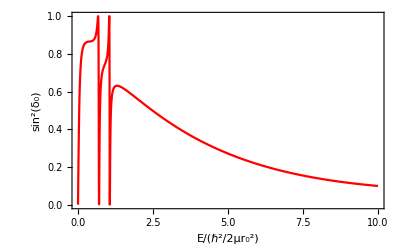

```mathematica
Plot[RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ][[3]],{ϵ,0.0001,ΔV0},Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"},PlotRange->{0,1}]
```

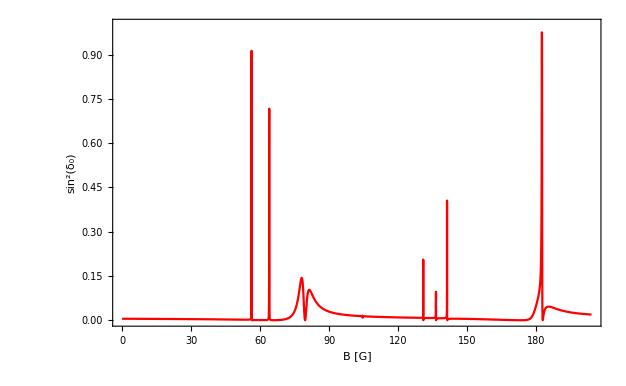

```mathematica
Energy=0.01;Boffset=78;
DysprosiumPlot=Plot[RunMagneticLoop[NCHAN,NumOpen,NumEven,L,rmatch,B02,Bfield-Boffset,γ,Energy,ϵi0[[1]]][[1]][[3]],{Bfield,0,Boffset+1.2B02},Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"B [G]","sin^2(δ_0)"},PlotRange->{0,1},PlotPoints->100]
```

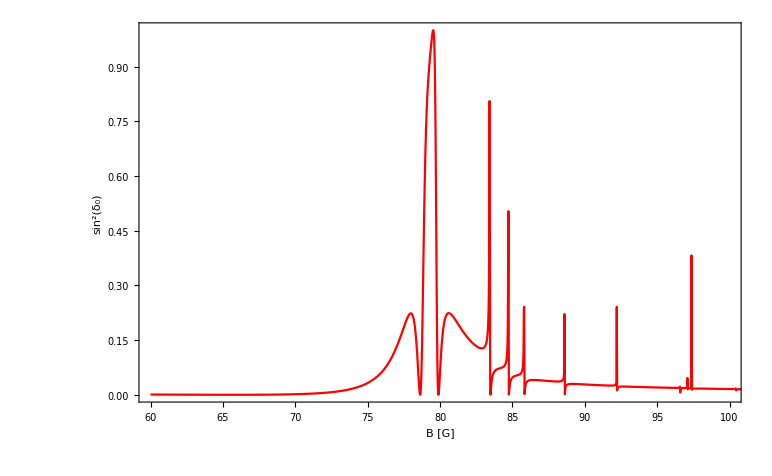

```mathematica
Show[DysprosiumPlot,PlotRange->{{60,100},{0,1}}]
```

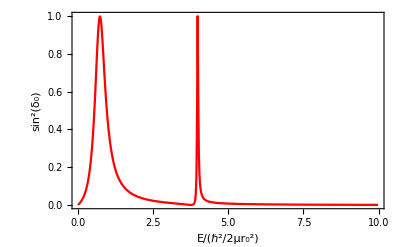
```mathematica
dataArray=Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data[[n]]},{n,1,3}],{ϵ,0.0001,Emax,Emax/500.0}];
ptest=ListPlot[Transpose[dataArray][[3]],Joined->True,Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"},PlotRange->{0,1}]
-Graphics-
```

Table::iterb: Iterator {ϵ,0.0001,Emax,0.002 Emax} does not have appropriate bounds.

Part::partw: Part 3 of Transpose[Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data⟦n⟧},{n,1,3}],{ϵ,0.0001,Emax,0.002 Emax}]] does not exist.

Table::iterb: Iterator {ϵ,0.0001,Emax,0.002 Emax} does not have appropriate bounds.

Part::partw: Part 3 of Transpose[Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data⟦n⟧},{n,1,3}],{ϵ,0.0001,Emax,0.002 Emax}]] does not exist.

Table::iterb: Iterator {ϵ,0.0001,Emax,0.002 Emax} does not have appropriate bounds.

Part::partw: Part 3 of Transpose[Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data⟦n⟧},{n,1.,3.}],{ϵ,0.0001,Emax,0.002 Emax}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {ϵ,0.0001,Emax,0.002 Emax} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Transpose[Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data⟦n⟧},{n,1.,3.}],{ϵ,0.0001,Emax,0.002 Emax}]]⟦3⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data⟦n⟧},{n,1,3}],{ϵ,0.0001,Emax,0.002 Emax}]]⟦3⟧,Joined→True,Frame→True,PlotStyle→RGBColor[1, 0, 0],LabelStyle→Large,FrameLabel→{E/(ℏ^2/2μr_0^2),sin^2(δ_0)},PlotRange→{0,1}]

-Graphics-

### Import data from the fortran runs

```mathematica
zclosedata = Import["~/Code/Nchannel/Square/CODES/MagneticF/fort.100","Table"];
zpa=DeleteCases[zclosedata[[3;;Length[zclosedata]]],{}];
ListContourPlot[zpa,PlotRange->All,FrameLabel->{"Energy [ℏ^2/2μr_0^2]","B [G]"},LabelStyle->Large,PlotRange->{0,1},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

### Use the following for a single energy but with varying B

```mathematica
padding={{100,10},Automatic};
```

```mathematica
thresholddata=Import["~/Code/Nchannel/Square/CODES/MagneticF/fort.100","Table"];
```

```mathematica
mfdata=Table[{thresholddata[[ib,2]],thresholddata[[ib,3]]},{ib,1,Length[thresholddata]}];
```

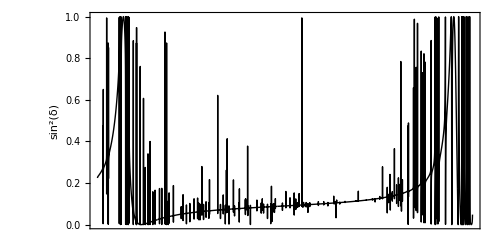

```mathematica
DyPlot1=ListPlot[mfdata,Joined->True,PlotStyle->{Thin,Black},LabelStyle->Large,Frame->True,FrameTicks->{None,Automatic},FrameLabel->{None,"sin^2(δ)"},PlotRange->All,ImageSize->{500,250},ImagePadding->padding,AspectRatio->Full]
```

```mathematica
bsdata=Table[Table[{thresholddata[[ib,2]],thresholddata[[ib,ie]]},{ib,1,Length[thresholddata]}],{ie,4,5}];
```

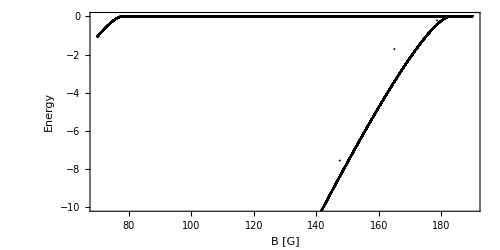

```mathematica
DyPlot2=ListPlot[bsdata,Joined->False,PlotStyle->Black,LabelStyle->Large,Frame->True,FrameLabel->{"B [G]","Energy"},PlotRange->{-10,0},ImageSize->{500,250},ImagePadding->{{100,10},{60,10}},AspectRatio->Full]
```

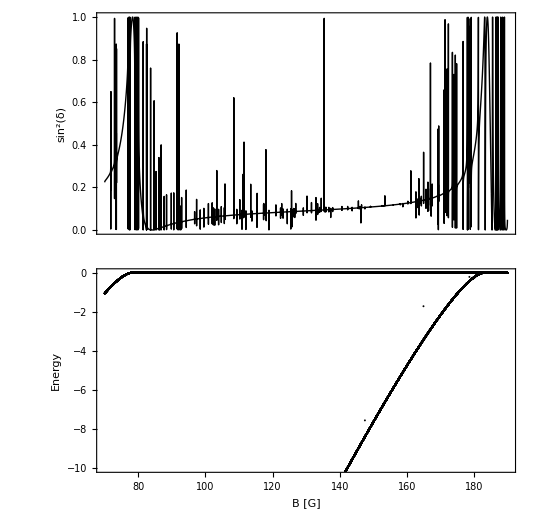

```mathematica
pmf1=GraphicsColumn[{DyPlot1,DyPlot2},Spacings->0]
```

```mathematica
Export["~/posters&talks/DAMOP-2018/figures/MagneticF1.pdf" ,pmf1]
```

~/posters&talks/DAMOP-2018/figures/MagneticF1.pdf

```mathematica
Export["~/posters&talks/DAMOP-2018/figures/MagneticF1-Dy.pdf",DyPlot1]
```

~/posters&talks/DAMOP-2018/figures/MagneticF1-Dy.pdf

```mathematica
Export["~/posters&talks/DAMOP-2018/figures/MagneticF2-Dy.pdf",DyPlot2]
```

~/posters&talks/DAMOP-2018/figures/MagneticF2-Dy.pdf